```mathematica
(*Измерение спектра источника*)
A={145862.6,350.0,771.2,179.6,26.2,33.0,70.8,109.8,151.0,178.6,196.8,183.8,143.0,83.6,47.8,23.2,10.8,5.8,6.0,4.6}
```

{145863.,350.,771.2,179.6,26.2,33.,70.8,109.8,151.,178.6,196.8,183.8,143.,83.6,47.8,23.2,10.8,5.8,6.,4.6}

```mathematica
A*0.08
```

{11669.,28.,61.696,14.368,2.096,2.64,5.664,8.784,12.08,14.288,15.744,14.704,11.44,6.688,3.824,1.856,0.864,0.464,0.48,0.368}

```mathematica
X=Array[#*0.5&,20,0]
```

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5}

```mathematica
Spectre=Transpose[{X}].({{1, 0}})+Transpose[{A}].({{0, 1}})
```

{{0.,145863.},{0.5,350.},{1.,771.2},{1.5,179.6},{2.,26.2},{2.5,33.},{3.,70.8},{3.5,109.8},{4.,151.},{4.5,178.6},{5.,196.8},{5.5,183.8},{6.,143.},{6.5,83.6},{7.,47.8},{7.5,23.2},{8.,10.8},{8.5,5.8},{9.,6.},{9.5,4.6}}

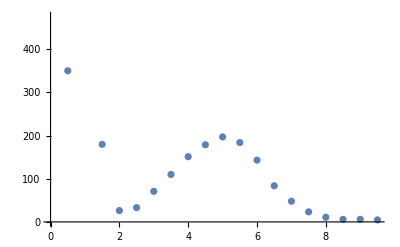

```mathematica
ListPlot[Spectre]
```

```mathematica
data=Spectre[[5;;20]]
```

{{2.,26.2},{2.5,33.},{3.,70.8},{3.5,109.8},{4.,151.},{4.5,178.6},{5.,196.8},{5.5,183.8},{6.,143.},{6.5,83.6},{7.,47.8},{7.5,23.2},{8.,10.8},{8.5,5.8},{9.,6.},{9.5,4.6}}

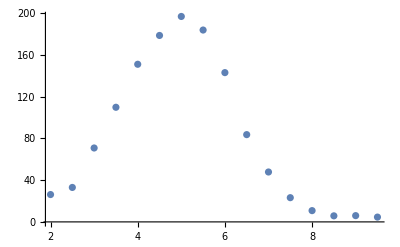

```mathematica
ListPlot[data]
```

```mathematica
errors=(A*0.08)[[5;;20]];
ampl Evaluate[PDF[NormalDistribution[x0,sigma],x]]
nlm=NonlinearModelFit[data,ampl Evaluate[PDF[NormalDistribution[x0,sigma],x]],{ampl,x0,sigma},{x}, Weights->1/errors];
GaussianFit=nlm["BestFit"]
nlm["ParameterTable"]
```

(ampl ⅇ^(-(x-x0)^2/(2 sigma^2)))/(√(2 π) sigma)

192.906 ⅇ^(-0.289343 (-4.87281+x)^2)

| Estimate | Standard Error | t-Statistic | P-Value
ampl | 635.644 | 18.8358 | 33.7465 | 4.79036×10^-14
x0 | 4.87281 | 0.0404714 | 120.401 | 3.36272×10^-21
sigma | 1.31455 | 0.0325766 | 40.3527 | 4.7859×10^-15

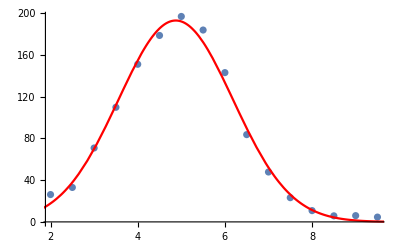

```mathematica
Show[ListPlot[data],Plot[GaussianFit,{x,0,10},PlotStyle->Red]]
```

```mathematica
Reduce[D[GaussianFit,x]==0]
```

x==4.87281

```mathematica
Coef1=ampl/(√(2π)sigma);
sigmaX=Sqrt[D[Coef1,ampl]^2*18.84^2+D[Coef1,sigma]^2*0.033^2]/.{ampl-> 635.64,sigma->1.314}
```

7.49724

```mathematica
(*Измерение резонансного поглощения*)
```

```mathematica
Sn100A=({{1, 1.44, 871.7, 1.52, 853.3}, {2, 1.52, 852.1, 1.61, 850.1}, {3, 1.48, 858.4, 1.59, 843.1}, {4, 1.37, 852.4, 1.51, 853.6}, {5, 1.21, 834.4, 1.35, 842.6}, {6, 4.44, 856.6, 4.71, 848.4}, {7, 3.71, 845.9, 3.92, 846.7}, {8, 3.08, 857.9, 3.27, 840.0}, {9, 2.48, 847.0, 2.64, 750.8}, {10, 2.12, 841.9, 1.67, 838.1}, {11, 1.57, 858.0, 1.64, 837.1}, {12, 1.55, 841.3, 1.16, 841.4}, {13, 1.06, 857.6, 2.79, 764.0}, {14, 2.62, 869.2, 3.00, 793.3}, {15, 2.83, 869.1, 3.16, 812.6}, {16, 2.99, 852.9, 3.49, 828.7}, {17, 2.16, 850.5, 3.12, 815.8}, {18, 1.85, 856.1, 2.82, 778.5}, {19, 2.34, 854.7, 2.32, 762.0}, {20, 2.11, 858.0, 1.99, 812.8}, {21, 1.93, 838.0, 2.48, 755.3}, {22, 2.25, 845.6, 2.22, 792.8}, {23, 3.28, 849.8, 2.04, 799.9}, {24, 2.94, 847.7, 2.41, 764.4}, {25, 2.66, 855.3, 2.24, 791.3}});
Sn100=Transpose[{Join[-Sn100A[[All,2]],Sn100A[[All,4]]]}].({{1, 0}})+
Transpose[{Join[Sn100A[[All,3]],Sn100A[[All,5]]]}].({{0, 1}});
Sn200A=({{1, 2.67, 384.7, 2.83, 314.1}, {2, 3.09, 382.7, 3.26, 347.2}, {3, 3.50, 385.8, 3.73, 372.8}, {4, 3.90, 380.3, 4.14, 372.4}, {5, 4.32, 384.4, 4.55, 374.1}, {6, 2.44, 379.3, 2.61, 311.5}, {7, 1.65, 381.8, 1.70, 366.7}, {8, 1.99, 385.8, 2.12, 329.0}, {9, 2.70, 382.2, 2.84, 324.7}, {10, 2.93, 368.9, 3.12, 342.6}, {11, 3.04, 371.2, 3.24, 365.9}, {12, 2.67, 379.3, 2.82, 327.2}, {13, 2.43, 379.6, 2.56, 317.5}, {14, 2.17, 380.6, 2.31, 313.9}, {15, 1.94, 372.2, 2.07, 338.1}, {16, 1.72, 373.9, 1.85, 346.9}, {17, 1.45, 390.0, 1.54, 360.9}, {18, 1.14, 384.6, 1.20, 379.5}, {19, 0.70, 375.7, 0.77, 371.8}, {20, 1.65, 396.0, 1.77, 358.3}, {21, 1.90, 374.7, 2.04, 337.1}});

Sn200=Transpose[{Join[-Sn200A[[All,2]],Sn200A[[All,4]]]}].({{1, 0}})+
Transpose[{Join[Sn200A[[All,3]],Sn200A[[All,5]]]}].({{0, 1}});
SnO2A=({{1, 0.72, 610.6, 0.76, 619.4}, {2, 0.87, 606.0, 0.93, 628.5}, {3, 1.14, 654.2, 1.21, 667.1}, {4, 1.43, 686.3, 1.53, 692.2}, {5, 1.29, 673.3, 1.38, 682.8}, {6, 1.06, 652.9, 1.23, 669.3}, {7, 2.80, 743.4, 2.98, 758.8}, {8, 3.42, 757.9, 3.59, 758.1}, {9, 4.12, 750.2, 4.37, 769.7}, {10, 4.50, 751.7, 4.77, 772.0}, {11, 2.51, 739.3, 2.64, 744.0}, {12, 2.24, 745.6, 2.39, 750.5}, {13, 1.65, 704.4, 1.76, 728.2}, {14, 1.08, 661.9, 1.16, 649.2}, {15, 0.33, 550.3, 0.39, 556.9}, {16, 0.21, 544.0, 0.25, 546.3}, {17, 0.48, 565.8, 0.53, 591.6}, {18, 0.73, 603.3, 0.75, 611.1}});
SnO2=Transpose[{Join[-SnO2A[[All,2]],SnO2A[[All,4]]]}].({{1, 0}})+
Transpose[{Join[SnO2A[[All,3]],SnO2A[[All,5]]]}].({{0, 1}});
```

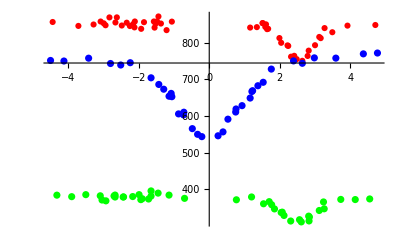

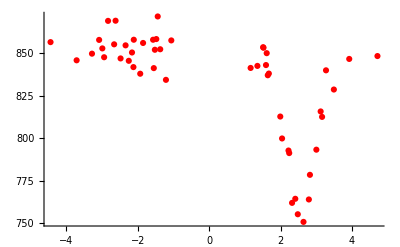

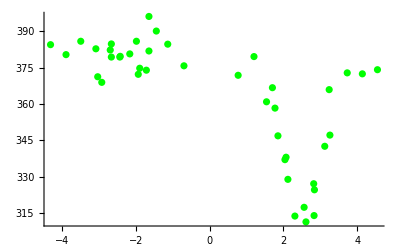

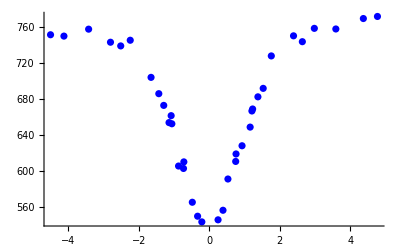

```mathematica
Show[
ListPlot[Sn100, PlotStyle->Red],
ListPlot[Sn200,PlotStyle->Green],
ListPlot[SnO2,PlotStyle->Blue], PlotRange->All
]
ListPlot[Sn100, PlotStyle->Red]
ListPlot[Sn200,PlotStyle->Green]
ListPlot[SnO2,PlotStyle->Blue]
```

```mathematica
(*mxSn100=Max[Sn100[[All,2]]];
mxSn200=Max[Sn200[[All,2]]];
mxSnO2=Max[SnO2[[All,2]]];
For[i=1,i≤ Length[Sn100],i++,
Sn100[[i,2]]=Sn100[[i,2]]*(-1)+mxSn100;
]
For[i=1,i≤ Length[Sn200],i++,
Sn200[[i,2]]=Sn200[[i,2]]*(-1)+mxSn200;
]
For[i=1,i≤ Length[SnO2],i++,
SnO2[[i,2]]=SnO2[[i,2]]*(-1)+mxSnO2;
]*)
```

```mathematica
Show[ListPlot[Sn100, PlotStyle->Red],ListPlot[Sn200,PlotStyle->Green],ListPlot[SnO2,PlotStyle->Blue],PlotRange->All]
```

-Graphics-

```mathematica
Lorenz[y0_,xc_,w_,Amp_,x_]:=y0+(2*Amp)*w/(4(x-xc)^2+(w)^2);
Sn100Approx=NonlinearModelFit[Sn100,Lorenz[y0,xc,w,Amp,x],{y0,xc,w,Amp},{x}];
```

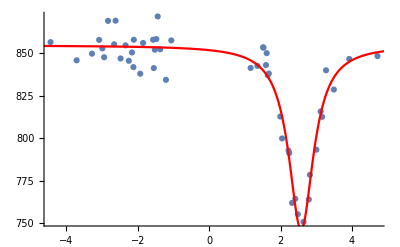

854.701-77.1373/(0.711312+4 (-2.57219+x)^2)

| Estimate | Standard Error | t-Statistic | P-Value
y0 | 854.701 | 1.68705 | 506.623 | 7.84076×10^-88
xc | 2.57219 | 0.0183634 | 140.071 | 3.60289×10^-62
w | 0.843393 | 0.0691018 | 12.2051 | 4.99291×10^-16
Amp | -45.7303 | 2.99651 | -15.2612 | 1.26925×10^-19

{y0→854.701,xc→2.57219,w→0.843393,Amp→-45.7303}

```mathematica
Show[ListPlot[Sn100],Plot[Sn100Approx["BestFit"],{x,-5,5},PlotRange->All,PlotStyle->Red]]
Sn100Approx["BestFit"]
Sn100Approx["ParameterTable"]
Sn100Approx["BestFitParameters"]
```

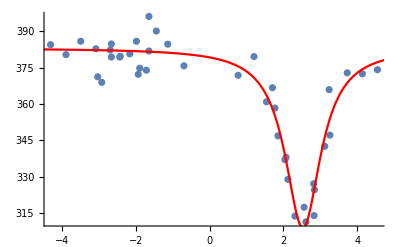

382.951-102.463/(1.38771+4 (-2.52657+x)^2)

| Estimate | Standard Error | t-Statistic | P-Value
y0 | 382.951 | 1.87346 | 204.408 | 2.30726×10^-47
xc | 2.52657 | 0.0271496 | 93.061 | 1.80775×10^-37
w | 1.17801 | 0.111218 | 10.5919 | 1.76209×10^-11
Amp | -43.4897 | 3.64127 | -11.9436 | 1.01594×10^-12

{y0→382.951,xc→2.52657,w→1.17801,Amp→-43.4897}

```mathematica
Sn200Approx=NonlinearModelFit[Sn200[[10;;42]],Lorenz[y0,xc,w,Amp,x],{y0,xc,w,Amp},{x}];
Show[ListPlot[Sn200],Plot[Sn200Approx["BestFit"],{x,-5,5},PlotRange->All,PlotStyle->Red]]
Sn200Approx["BestFit"]
Sn200Approx["ParameterTable"]
Sn200Approx["BestFitParameters"]
```

36

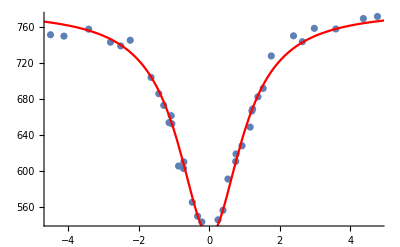

778.678-1147.23/(4.59169+4 (-0.0059024+x)^2)

| Estimate | Standard Error | t-Statistic | P-Value
y0 | 778.678 | 5.25471 | 148.187 | 2.26559×10^-22
xc | 0.0059024 | 0.0219995 | 0.268298 | 0.79268
w | -2.14282 | 0.116407 | -18.4079 | 1.0789×10^-10
Amp | 267.69 | 14.8247 | 18.057 | 1.37353×10^-10

{y0→778.678,xc→0.0059024,w→-2.14282,Amp→267.69}

```mathematica
Length[SnO2]
SnO2Approx=NonlinearModelFit[SnO2[[10;;26]],Lorenz[y0,xc,w,Amp,x],{y0,xc,w,Amp},{x}];
Show[ListPlot[SnO2],Plot[SnO2Approx["BestFit"],{x,-5,5},PlotRange->All,PlotStyle->Red]]
SnO2Approx["BestFit"]
SnO2Approx["ParameterTable"]
SnO2Approx["BestFitParameters"]
```